## S-shape vs L-shape

```mathematica
A=10;
α1=0.4;
s1=0.1;
s2=0.2;
s3=10;
d=2;
```

```mathematica
f[kP_]:=A kP^α1;
sf[kP_]:=s1+(s2-s1)/(1+ⅇ^(-s3 (kP-d)));
```

```mathematica
dkPdt:=sf[kP] f[kP]
```

Changing parameter A

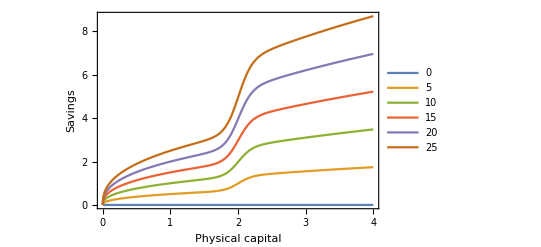

```mathematica
α1=0.4;
s1=0.1;
s2=0.2;
s3=10;
d=2;
ValuesA={0, 5,10,15,20,25};
Plot[Evaluate[Table[dkPdt, {A, ValuesA}]], {kP,0,4},
Frame->True, FrameLabel->{"Physical capital", "Savings"},
PlotLegends->ValuesA]
```

A: exogenous level of technology
Higher A increases savings
No influence on S-shape, except when A=0

### Changing parameter α1

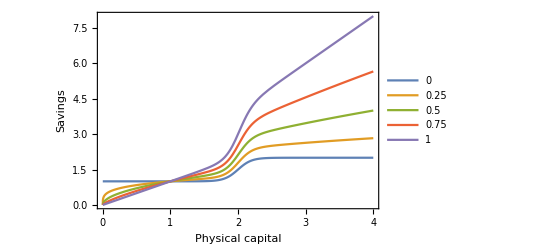

```mathematica
A=10;
s1=0.1;
s2=0.2;
s3=10;
d=2;
Valuesα1={0, 0.25,0.5,0.75,1};
Plot[Evaluate[Table[dkPdt, {α1, Valuesα1}]], {kP,0,4},
Frame->True, FrameLabel->{"Physical capital", "Savings"},
PlotLegends->Valuesα1]
```

α1: output elasticity of capital
No influence on S-shape

### Changing parameter s1

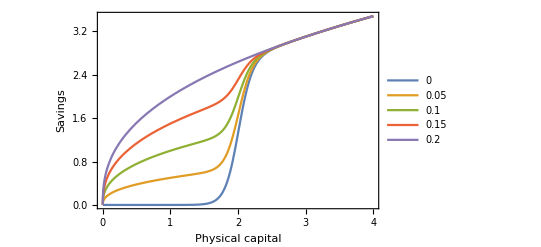

```mathematica
α1=0.4;
s1=0.1;
s2=0.2;
s3=10;
d=2;
Valuess1={0,0.05,0.1,0.15,0.2};
Plot[Evaluate[Table[dkPdt, {s1, Valuess1}]], {kP,0,4},
Frame->True, FrameLabel->{"Physical capital", "Savings"},
PlotLegends->Valuess1]
```

s1: initial saving rate before threshold d
S-shape if s1 < s2
L-shape if s1 = s2

### Changing parameter s2

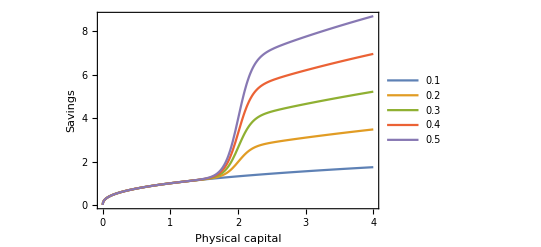

```mathematica
A=10;
α1=0.4;
s1=0.1;
s3=10;
d=2;
Valuess2={0.1,0.2,0.3,0.4,0.5};
Plot[Evaluate[Table[dkPdt, {s2, Valuess2}]], {kP,0,4},
Frame->True, FrameLabel->{"Physical capital", "Savings"},
PlotLegends->Valuess2]
```

s2: savings rate after threshold d
S-shape if s2 > s1
L-shape if s2 = s1

### Changing parameter s3

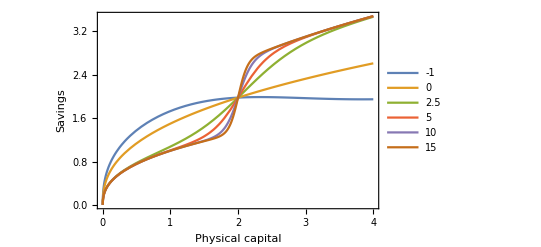

```mathematica
A=10;
α1=0.4;
s1=0.1;
s2=0.2;
d=2;
Valuess3={-1,0,2.5,5,10,15};
Plot[Evaluate[Table[dkPdt, {s3, Valuess3}]], {kP,0,4},
Frame->True, FrameLabel->{"Physical capital", "Savings"},
PlotLegends->Valuess3]
```

S-shape if s3 > 0
L-shape if s3 <= 0

### Changing parameter d

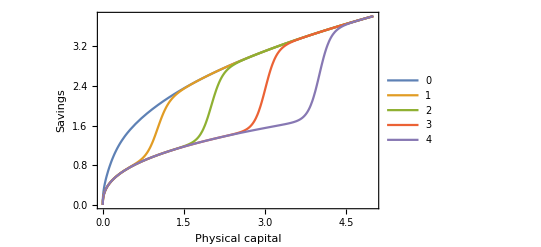

```mathematica
A=10;
α1=0.4;
s1=0.1;
s2=0.2;
s3=10;
Valuesd={0,1,2,3,4};
Plot[Evaluate[Table[dkPdt, {d, Valuesd}]], {kP,0,5},
Frame->True, FrameLabel->{"Physical capital", "Savings"},
PlotLegends->Valuesd]
```

d is where the S-shape occurs